For  the unCoVer project - Colombia was used  the  databases published daily by the INS-Colombia. This database includes  the national detected cases infected with SARS-CoV-2 since the start of the pandemic in march 2020 until today. You could contact me to lina.ruiz2@udea.edu.co if you want a complete file with all the downloaded databases used here.  In this notebook is selected the hospitalized cases with defined outcome, and it is identified the first admission date to hospital or ICU and the discharge date (i.e., recovery or home) or death

In this notebook we will analyze only the cases that go to Hospital and/or UCI ans have a defined outcome...we estimated the admission dates

In the analysis of the next data bases (i.e. After 3/10/2020) it will be included other cases. And it is NECESSARY to analyze what it is already reported about them in the previous matrices

### Exploring the matrices

```mathematica
SetDirectory["/home/lina/Documents/datos_INS"];
```

```mathematica
matrix1=Import["dataStructue_15_200.m"];
matrix2=Import["dataStructue_201_210.m"];
matrix3=Import["dataStructue_211_220.m"];
```

```mathematica
m1=SortBy[matrix1//Normal,First];
m2=SortBy[matrix2//Normal,First];
m3=SortBy[matrix3//Normal,First];
```

```mathematica
allMs=Flatten[{m1,m2,m3},1];
```

```mathematica
numPad=Table[StringJoin["0",i],{i,ToString/@Range[1,9]}];dia={numPad,Range[10,31]}//Flatten//ToString/@#&;mes={numPad[[3;;]],Range[10,12]}//Flatten//ToString/@#&;
fecha=Table[a<>"-"<>m<>"-"<>d,{a,{"2020","2021"}},{m,mes},{d,dia}]//Flatten;(*La fecha minima está en la posicion 15. la data del INS de la fecha en la posicon 14 no tiene la columna ubicación y sale un fecha[["NotFound"]]*)
```

```mathematica
fecha[[220]]
```

2020-10-03

```mathematica
masterM={{"fecha",Sequence@@Table["caso"<>ToString@i,{i,1,Length[allMs[[-1]]]}]},Sequence@@Map[PadRight[#,Length[allMs[[-1]]],""]&,allMs]};(* Matrix with the name of the columns*)
```

```mathematica
Grid[masterM[[45;;55,4250;;4265]]]
```

Casa | Casa | Hospital | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Fallecido
Casa | Casa | Hospital | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Fallecido
Casa | Casa | Hospital | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Fallecido
Casa | Casa | Hospital | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Fallecido
Casa | Casa | Hospital | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Fallecido
Casa | Casa | Hospital | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Fallecido
Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa

```mathematica
(*ESTA ES LA MATRIZ CORREGIDA AL ELIMINAR LOS CASOS QUE SE PERDIERON 4150-4900*)
```

```mathematica
masterM=Import["/home/lina/Documents/datos_INS/masterMcorregida.m"];
```

```mathematica
Grid[masterM[[45;;55,4250;;4265]]]
```

|  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa

### Exploring the corrected matrix

```mathematica
Grid[masterM[[All,1]]]
```

Grid[{fecha,2020-03-15,2020-03-16,2020-03-17,2020-03-18,2020-03-19,2020-03-20,2020-03-21,2020-03-22,2020-03-23,2020-03-24,2020-03-25,2020-03-26,2020-03-27,2020-03-28,2020-03-29,2020-03-30,2020-03-31,2020-04-01,2020-04-02,2020-04-03,2020-04-04,2020-04-05,2020-04-06,2020-04-07,2020-04-08,2020-04-09,2020-04-10,2020-04-12,2020-04-13,2020-04-14,2020-04-15,2020-04-16,2020-04-17,2020-04-18,2020-04-19,2020-04-20,2020-04-21,2020-04-22,2020-04-23,2020-04-24,2020-04-25,2020-04-26,2020-04-27,2020-04-28,2020-04-29,2020-04-30,2020-05-01,2020-05-02,2020-05-03,2020-05-04,2020-05-05,2020-05-06,2020-05-07,2020-05-08,2020-05-09,2020-05-10,2020-05-11,2020-05-12,2020-05-13,2020-05-14,2020-05-15,2020-05-16,2020-05-17,2020-05-18,2020-05-19,2020-05-20,2020-05-21,2020-05-22,2020-05-23,2020-05-24,2020-05-25,2020-05-26,2020-05-27,2020-05-28,2020-05-29,2020-05-30,2020-05-31,2020-06-01,2020-06-02,2020-06-03,2020-06-04,2020-06-05,2020-06-06,2020-06-07,2020-06-08,2020-06-09,2020-06-10,2020-06-11,2020-06-12,2020-06-13,2020-06-14,2020-06-15,2020-06-16,2020-06-17,2020-06-18,2020-06-19,2020-06-20,2020-06-21,2020-06-22,2020-06-23,2020-06-24,2020-06-25,2020-06-26,2020-06-27,2020-06-28,2020-06-29,2020-06-30,2020-07-01,2020-07-02,2020-07-03,2020-07-04,2020-07-05,2020-07-06,2020-07-07,2020-07-08,2020-07-09,2020-07-10,2020-07-11,2020-07-12,2020-07-13,2020-07-14,2020-07-15,2020-07-16,2020-07-17,2020-07-18,2020-07-19,2020-07-20,2020-07-21,2020-07-22,2020-07-23,2020-07-24,2020-07-25,2020-07-26,2020-07-27,2020-07-28,2020-07-29,2020-07-30,2020-07-31,2020-08-01,2020-08-02,2020-08-03,2020-08-04,2020-08-05,2020-08-06,2020-08-07,2020-08-08,2020-08-09,2020-08-10,2020-08-11,2020-08-12,2020-08-13,2020-08-14,2020-08-15,2020-08-16,2020-08-17,2020-08-18,2020-08-19,2020-08-20,2020-08-21,2020-08-22,2020-08-23,2020-08-24,2020-08-25,2020-08-26,2020-08-27,2020-08-28,2020-08-29,2020-08-30,2020-08-31,2020-09-01,2020-09-02,2020-09-03,2020-09-04,2020-09-05,2020-09-06,2020-09-07,2020-09-08,2020-09-09,2020-09-10,2020-09-11,2020-09-12,2020-09-13,2020-09-14,2020-09-15,2020-09-16,2020-09-17,2020-09-18,2020-09-19,2020-09-20,2020-09-21,2020-09-22,2020-09-23,2020-09-24,2020-09-25,2020-09-26,2020-09-27,2020-09-28,2020-09-29,2020-09-30,2020-10-01,2020-10-02,2020-10-03}]

```mathematica
Grid[masterM[[All,4250]]]
```

Grid[{caso4249,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido}]

```mathematica
Grid[masterM[[All,4251]]]
```

Grid[{caso4250,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Casa,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Casa,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa}]

```mathematica
Grid[masterM[[All,4750]]]
```

Grid[{caso4749,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,Hospital,Hospital,Hospital,Hospital,Hospital,Hospital,Hospital,Casa,Casa,Casa,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Casa,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Casa,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Recuperado,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa}]

```mathematica
(************Revisando que los casos tengan el LABEL adecuado*)
```

```mathematica
keysCases=ToExpression[StringTake[#,5;;-1]&/@masterM[[1,2;;]]]//ToExpression
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,1048372,1048455,1048456,1048457,1048458,1048459,1048460,1048461,1048462,1048463,1048464,1048465,1048466,1048467,1048468,1048469,1048470,1048471,1048472,1048473,1048474,1048475,1048476,1048477,1048478,1048479,1048480,1048481,1048482,1048483,1048484,1048485,1048486,1048487,1048488,1048489,1048490,1048491,1048492,1048493,1048494,1048495,1048496,1048497,1048498,1048499,1048500,1048501,1048502,1048503,1048504,1048505,1048506,1048507,1048508,1048509,1048510,1048511,1048512,1048513,1048514,1048515,1048516,1048517,1048518,1048519,1048520,1048521,1048522,1048523,1048524,1048525,1048526,1048527,1048528,1048529,1048530,1048531,1048532,1048533,1048534,1048535,1048536}
 |  |  |  |

```mathematica
Complement[Range[1,keysCases//Length]//N,keysCases//N]
```

{}

```mathematica
dataForlabels=Import["2020-09-24.xlsx"];
```

```mathematica
dataForlabels//Dimensions
```

{1,790824,22}

```mathematica
Complement[Range[1,(DeleteCases[dataForlabels[[1,All,1]],""]//Length)-1]//N,dataForlabels[[1,All,1]]//N]
```

{4156.,4157.,4158.,4159.,4160.,4161.,4162.,4163.,4164.,4165.,4166.,4167.,4168.,4169.,4174.,4405.,4406.,4407.,4408.,4409.,4410.,4411.,4452.,4453.,4454.,4596.,4597.,4598.,4599.,4600.,4601.,4602.,4603.,4604.,4605.,4606.,4607.,4608.,4609.,4866.}

```mathematica
labels=dataForlabels[[1,All,1]];
```

```mathematica
labels[[1]]
```

```mathematica
(*************************************************************+)
```

```mathematica
Grid[masterM[[All,{1,4750}]]]
```

fecha | caso4749
2020-03-15 | 
2020-03-16 | 
2020-03-17 | 
2020-03-18 | 
2020-03-19 | 
2020-03-20 | 
2020-03-21 | 
2020-03-22 | 
2020-03-23 | 
2020-03-24 | 
2020-03-25 | 
2020-03-26 | 
2020-03-27 | 
2020-03-28 | 
2020-03-29 | 
2020-03-30 | 
2020-03-31 | 
2020-04-01 | 
2020-04-02 | 
2020-04-03 | 
2020-04-04 | 
2020-04-05 | 
2020-04-06 | 
2020-04-07 | 
2020-04-08 | 
2020-04-09 | 
2020-04-10 | 
2020-04-12 | 
2020-04-13 | 
2020-04-14 | 
2020-04-15 | 
2020-04-16 | 
2020-04-17 | 
2020-04-18 | 
2020-04-19 | 
2020-04-20 | 
2020-04-21 | 
2020-04-22 | 
2020-04-23 | 
2020-04-24 | 
2020-04-25 | 
2020-04-26 | 
2020-04-27 | 
2020-04-28 | 
2020-04-29 | 
2020-04-30 | 
2020-05-01 | 
2020-05-02 | 
2020-05-03 | 
2020-05-04 | Hospital
2020-05-05 | Hospital
2020-05-06 | Hospital
2020-05-07 | Hospital
2020-05-08 | Hospital
2020-05-09 | Hospital
2020-05-10 | Hospital
2020-05-11 | Casa
2020-05-12 | Casa
2020-05-13 | Casa
2020-05-14 | Recuperado
2020-05-15 | Recuperado
2020-05-16 | Recuperado
2020-05-17 | Recuperado
2020-05-18 | Recuperado
2020-05-19 | Recuperado
2020-05-20 | Recuperado
2020-05-21 | Recuperado
2020-05-22 | Recuperado
2020-05-23 | Recuperado
2020-05-24 | Recuperado
2020-05-25 | Recuperado
2020-05-26 | Recuperado
2020-05-27 | Recuperado
2020-05-28 | Recuperado
2020-05-29 | Recuperado
2020-05-30 | Recuperado
2020-05-31 | Recuperado
2020-06-01 | Recuperado
2020-06-02 | Recuperado
2020-06-03 | Recuperado
2020-06-04 | Recuperado
2020-06-05 | Recuperado
2020-06-06 | Recuperado
2020-06-07 | Recuperado
2020-06-08 | Recuperado
2020-06-09 | Recuperado
2020-06-10 | Recuperado
2020-06-11 | Recuperado
2020-06-12 | Recuperado
2020-06-13 | Recuperado
2020-06-14 | Recuperado
2020-06-15 | Recuperado
2020-06-16 | Recuperado
2020-06-17 | Recuperado
2020-06-18 | Recuperado
2020-06-19 | Recuperado
2020-06-20 | Recuperado
2020-06-21 | Recuperado
2020-06-22 | Recuperado
2020-06-23 | Recuperado
2020-06-24 | Recuperado
2020-06-25 | Recuperado
2020-06-26 | Recuperado
2020-06-27 | Recuperado
2020-06-28 | Recuperado
2020-06-29 | Recuperado
2020-06-30 | Recuperado
2020-07-01 | Recuperado
2020-07-02 | Recuperado
2020-07-03 | Recuperado
2020-07-04 | Recuperado
2020-07-05 | Recuperado
2020-07-06 | Recuperado
2020-07-07 | Recuperado
2020-07-08 | Recuperado
2020-07-09 | Recuperado
2020-07-10 | Recuperado
2020-07-11 | Recuperado
2020-07-12 | Recuperado
2020-07-13 | Recuperado
2020-07-14 | Recuperado
2020-07-15 | Recuperado
2020-07-16 | Recuperado
2020-07-17 | Recuperado
2020-07-18 | Recuperado
2020-07-19 | Recuperado
2020-07-20 | Recuperado
2020-07-21 | Recuperado
2020-07-22 | Recuperado
2020-07-23 | Recuperado
2020-07-24 | Casa
2020-07-25 | Recuperado
2020-07-26 | Recuperado
2020-07-27 | Recuperado
2020-07-28 | Recuperado
2020-07-29 | Recuperado
2020-07-30 | Recuperado
2020-07-31 | Recuperado
2020-08-01 | Recuperado
2020-08-02 | Recuperado
2020-08-03 | Recuperado
2020-08-04 | Recuperado
2020-08-05 | Recuperado
2020-08-06 | Recuperado
2020-08-07 | Recuperado
2020-08-08 | Recuperado
2020-08-09 | Recuperado
2020-08-10 | Recuperado
2020-08-11 | Recuperado
2020-08-12 | Recuperado
2020-08-13 | Recuperado
2020-08-14 | Casa
2020-08-15 | Recuperado
2020-08-16 | Recuperado
2020-08-17 | Recuperado
2020-08-18 | Recuperado
2020-08-19 | Recuperado
2020-08-20 | Recuperado
2020-08-21 | Recuperado
2020-08-22 | Recuperado
2020-08-23 | Recuperado
2020-08-24 | Recuperado
2020-08-25 | Recuperado
2020-08-26 | Recuperado
2020-08-27 | Recuperado
2020-08-28 | Recuperado
2020-08-29 | Recuperado
2020-08-30 | Recuperado
2020-08-31 | Recuperado
2020-09-01 | Recuperado
2020-09-02 | Recuperado
2020-09-03 | Recuperado
2020-09-04 | Recuperado
2020-09-05 | Recuperado
2020-09-06 | Recuperado
2020-09-07 | Recuperado
2020-09-08 | Recuperado
2020-09-09 | Recuperado
2020-09-10 | Recuperado
2020-09-11 | Recuperado
2020-09-12 | Recuperado
2020-09-13 | Recuperado
2020-09-14 | Recuperado
2020-09-15 | Casa
2020-09-16 | Casa
2020-09-17 | Casa
2020-09-18 | Casa
2020-09-19 | Casa
2020-09-20 | Casa
2020-09-21 | Casa
2020-09-22 | Casa
2020-09-23 | Casa
2020-09-24 | Casa
2020-09-25 | Casa
2020-09-26 | Casa
2020-09-27 | Casa
2020-09-28 | Casa
2020-09-29 | Casa
2020-09-30 | Casa
2020-10-01 | Casa
2020-10-02 | Casa
2020-10-03 | Casa

```mathematica
caso4749=Import["/home/lina/Documents/datos_INS/2020-05-04.xlsx"];
```

```mathematica
caso4749//Dimensions
```

{1,7974,16}

```mathematica
caso4749[[1,4750]]
```

{4788.,Wed 22 Apr 2020 00:00:00GMT-5,11001.,Bogotá D.C.,Bogotá D.C.,54.,F,En estudio,Hospital,Moderado,Colombia,Sat 18 Apr 2020 00:00:00GMT-5,  -   -,Fri 24 Apr 2020 00:00:00GMT-5,  -   -,Fri 24 Apr 2020 00:00:00GMT-5}

```mathematica
caso4749=Import["/home/lina/Documents/datos_INS/2020-05-11.xlsx"];
```

```mathematica
caso4749//Dimensions
```

{1,11614,32}

```mathematica
caso4749[[1,4750]]
```

{4788.,Wed 22 Apr 2020 00:00:00GMT-5,11001.,Bogotá D.C.,Bogotá D.C.,54.,F,En estudio,Casa,Leve,Colombia,Sat 18 Apr 2020 00:00:00GMT-5,  -   -,Fri 24 Apr 2020 00:00:00GMT-5,  -   -,Fri 24 Apr 2020 00:00:00GMT-5,,,,,,,,,,,,,,,,}

```mathematica
(**************************************************+)
```

```mathematica
Grid[masterM[[All,{1,7000}]]]
```

fecha | caso6999
2020-03-15 | 
2020-03-16 | 
2020-03-17 | 
2020-03-18 | 
2020-03-19 | 
2020-03-20 | 
2020-03-21 | 
2020-03-22 | 
2020-03-23 | 
2020-03-24 | 
2020-03-25 | 
2020-03-26 | 
2020-03-27 | 
2020-03-28 | 
2020-03-29 | 
2020-03-30 | 
2020-03-31 | 
2020-04-01 | 
2020-04-02 | 
2020-04-03 | 
2020-04-04 | 
2020-04-05 | 
2020-04-06 | 
2020-04-07 | 
2020-04-08 | 
2020-04-09 | 
2020-04-10 | 
2020-04-12 | 
2020-04-13 | 
2020-04-14 | 
2020-04-15 | 
2020-04-16 | 
2020-04-17 | 
2020-04-18 | 
2020-04-19 | 
2020-04-20 | 
2020-04-21 | 
2020-04-22 | 
2020-04-23 | 
2020-04-24 | 
2020-04-25 | 
2020-04-26 | 
2020-04-27 | 
2020-04-28 | 
2020-04-29 | 
2020-04-30 | 
2020-05-01 | 
2020-05-02 | 
2020-05-03 | 
2020-05-04 | Casa
2020-05-05 | Casa
2020-05-06 | Casa
2020-05-07 | Casa
2020-05-08 | Casa
2020-05-09 | Casa
2020-05-10 | Casa
2020-05-11 | Casa
2020-05-12 | Casa
2020-05-13 | Fallecido
2020-05-14 | Fallecido
2020-05-15 | Fallecido
2020-05-16 | Fallecido
2020-05-17 | Fallecido
2020-05-18 | Fallecido
2020-05-19 | Fallecido
2020-05-20 | Fallecido
2020-05-21 | Fallecido
2020-05-22 | Fallecido
2020-05-23 | Fallecido
2020-05-24 | Fallecido
2020-05-25 | Fallecido
2020-05-26 | Fallecido
2020-05-27 | Fallecido
2020-05-28 | Fallecido
2020-05-29 | Fallecido
2020-05-30 | Fallecido
2020-05-31 | Fallecido
2020-06-01 | Fallecido
2020-06-02 | Fallecido
2020-06-03 | Fallecido
2020-06-04 | Fallecido
2020-06-05 | Fallecido
2020-06-06 | Fallecido
2020-06-07 | Fallecido
2020-06-08 | Fallecido
2020-06-09 | Fallecido
2020-06-10 | Fallecido
2020-06-11 | Fallecido
2020-06-12 | Fallecido
2020-06-13 | Fallecido
2020-06-14 | Fallecido
2020-06-15 | Fallecido
2020-06-16 | Fallecido
2020-06-17 | Fallecido
2020-06-18 | Fallecido
2020-06-19 | Fallecido
2020-06-20 | Fallecido
2020-06-21 | Fallecido
2020-06-22 | Fallecido
2020-06-23 | Fallecido
2020-06-24 | Fallecido
2020-06-25 | Fallecido
2020-06-26 | Fallecido
2020-06-27 | Fallecido
2020-06-28 | Fallecido
2020-06-29 | Fallecido
2020-06-30 | Fallecido
2020-07-01 | Fallecido
2020-07-02 | Fallecido
2020-07-03 | Fallecido
2020-07-04 | Fallecido
2020-07-05 | Fallecido
2020-07-06 | Fallecido
2020-07-07 | Fallecido
2020-07-08 | Fallecido
2020-07-09 | Fallecido
2020-07-10 | Fallecido
2020-07-11 | Fallecido
2020-07-12 | Fallecido
2020-07-13 | Fallecido
2020-07-14 | Fallecido
2020-07-15 | Fallecido
2020-07-16 | Fallecido
2020-07-17 | Fallecido
2020-07-18 | Fallecido
2020-07-19 | Fallecido
2020-07-20 | Fallecido
2020-07-21 | Fallecido
2020-07-22 | Fallecido
2020-07-23 | Fallecido
2020-07-24 | Fallecido
2020-07-25 | Fallecido
2020-07-26 | Fallecido
2020-07-27 | Fallecido
2020-07-28 | Fallecido
2020-07-29 | Fallecido
2020-07-30 | Fallecido
2020-07-31 | Fallecido
2020-08-01 | Fallecido
2020-08-02 | Fallecido
2020-08-03 | Fallecido
2020-08-04 | Fallecido
2020-08-05 | Fallecido
2020-08-06 | Fallecido
2020-08-07 | Fallecido
2020-08-08 | Fallecido
2020-08-09 | Fallecido
2020-08-10 | Fallecido
2020-08-11 | Fallecido
2020-08-12 | Fallecido
2020-08-13 | Fallecido
2020-08-14 | Fallecido
2020-08-15 | Fallecido
2020-08-16 | Fallecido
2020-08-17 | Fallecido
2020-08-18 | Fallecido
2020-08-19 | Fallecido
2020-08-20 | Fallecido
2020-08-21 | Fallecido
2020-08-22 | Fallecido
2020-08-23 | Fallecido
2020-08-24 | Fallecido
2020-08-25 | Fallecido
2020-08-26 | Fallecido
2020-08-27 | Fallecido
2020-08-28 | Fallecido
2020-08-29 | Fallecido
2020-08-30 | Fallecido
2020-08-31 | Fallecido
2020-09-01 | Fallecido
2020-09-02 | Fallecido
2020-09-03 | Fallecido
2020-09-04 | Fallecido
2020-09-05 | Fallecido
2020-09-06 | Fallecido
2020-09-07 | Fallecido
2020-09-08 | Fallecido
2020-09-09 | Fallecido
2020-09-10 | Fallecido
2020-09-11 | Fallecido
2020-09-12 | Fallecido
2020-09-13 | Fallecido
2020-09-14 | Fallecido
2020-09-15 | Fallecido
2020-09-16 | Fallecido
2020-09-17 | Fallecido
2020-09-18 | Fallecido
2020-09-19 | Fallecido
2020-09-20 | Fallecido
2020-09-21 | Fallecido
2020-09-22 | Fallecido
2020-09-23 | Fallecido
2020-09-24 | Fallecido
2020-09-25 | Fallecido
2020-09-26 | Fallecido
2020-09-27 | Fallecido
2020-09-28 | Fallecido
2020-09-29 | Fallecido
2020-09-30 | Fallecido
2020-10-01 | Fallecido
2020-10-02 | Fallecido
2020-10-03 | Fallecido

```mathematica
caso7000=Import["/home/lina/Documents/datos_INS/2020-05-12.xlsx"];
```

```mathematica
caso7000//Dimensions
```

{1,12273,32}

```mathematica
caso7000[[1,7000]]
```

{7039.,Mon 27 Apr 2020 00:00:00GMT-5,91001.,Amazonas,Leticia,58.,M,Importado,Casa,Leve,Brasil,Mon 27 Apr 2020 00:00:00GMT-5,  -   -,Sat 2 May 2020 00:00:00GMT-5,  -   -,Sat 2 May 2020 00:00:00GMT-5,,,,,,,,,,,,,,,,}

```mathematica
caso7000=Import["/home/lina/Documents/datos_INS/2020-05-13.xlsx"];
```

```mathematica
caso7000//Dimensions
```

{1,12931,30}

```mathematica
caso7000[[1,7000]]
```

{7039.,Mon 27 Apr 2020 00:00:00GMT-5,91001.,Amazonas,Leticia,58.,M,Importado,Fallecido,Fallecido,Brasil,Mon 27 Apr 2020 00:00:00GMT-5,Tue 12 May 2020 00:00:00GMT-5,Sat 2 May 2020 00:00:00GMT-5,  -   -,Sat 2 May 2020 00:00:00GMT-5,,,,,,,,,,,,,,}

```mathematica
(***********************************************)
```

```mathematica
(* PROBLEMAS CON EL CASO 500000*)
```

```mathematica
Grid[masterM[[All,{1,500000}]]]
```

fecha | caso499999
2020-03-15 | 
2020-03-16 | 
2020-03-17 | 
2020-03-18 | 
2020-03-19 | 
2020-03-20 | 
2020-03-21 | 
2020-03-22 | 
2020-03-23 | 
2020-03-24 | 
2020-03-25 | 
2020-03-26 | 
2020-03-27 | 
2020-03-28 | 
2020-03-29 | 
2020-03-30 | 
2020-03-31 | 
2020-04-01 | 
2020-04-02 | 
2020-04-03 | 
2020-04-04 | 
2020-04-05 | 
2020-04-06 | 
2020-04-07 | 
2020-04-08 | 
2020-04-09 | 
2020-04-10 | 
2020-04-12 | 
2020-04-13 | 
2020-04-14 | 
2020-04-15 | 
2020-04-16 | 
2020-04-17 | 
2020-04-18 | 
2020-04-19 | 
2020-04-20 | 
2020-04-21 | 
2020-04-22 | 
2020-04-23 | 
2020-04-24 | 
2020-04-25 | 
2020-04-26 | 
2020-04-27 | 
2020-04-28 | 
2020-04-29 | 
2020-04-30 | 
2020-05-01 | 
2020-05-02 | 
2020-05-03 | 
2020-05-04 | 
2020-05-05 | 
2020-05-06 | 
2020-05-07 | 
2020-05-08 | 
2020-05-09 | 
2020-05-10 | 
2020-05-11 | 
2020-05-12 | 
2020-05-13 | 
2020-05-14 | 
2020-05-15 | 
2020-05-16 | 
2020-05-17 | 
2020-05-18 | 
2020-05-19 | 
2020-05-20 | 
2020-05-21 | 
2020-05-22 | 
2020-05-23 | 
2020-05-24 | 
2020-05-25 | 
2020-05-26 | 
2020-05-27 | 
2020-05-28 | 
2020-05-29 | 
2020-05-30 | 
2020-05-31 | 
2020-06-01 | 
2020-06-02 | 
2020-06-03 | 
2020-06-04 | 
2020-06-05 | 
2020-06-06 | 
2020-06-07 | 
2020-06-08 | 
2020-06-09 | 
2020-06-10 | 
2020-06-11 | 
2020-06-12 | 
2020-06-13 | 
2020-06-14 | 
2020-06-15 | 
2020-06-16 | 
2020-06-17 | 
2020-06-18 | 
2020-06-19 | 
2020-06-20 | 
2020-06-21 | 
2020-06-22 | 
2020-06-23 | 
2020-06-24 | 
2020-06-25 | 
2020-06-26 | 
2020-06-27 | 
2020-06-28 | 
2020-06-29 | 
2020-06-30 | 
2020-07-01 | 
2020-07-02 | 
2020-07-03 | 
2020-07-04 | 
2020-07-05 | 
2020-07-06 | 
2020-07-07 | 
2020-07-08 | 
2020-07-09 | 
2020-07-10 | 
2020-07-11 | 
2020-07-12 | 
2020-07-13 | 
2020-07-14 | 
2020-07-15 | 
2020-07-16 | 
2020-07-17 | 
2020-07-18 | 
2020-07-19 | 
2020-07-20 | 
2020-07-21 | 
2020-07-22 | 
2020-07-23 | 
2020-07-24 | 
2020-07-25 | 
2020-07-26 | 
2020-07-27 | 
2020-07-28 | 
2020-07-29 | 
2020-07-30 | 
2020-07-31 | 
2020-08-01 | 
2020-08-02 | 
2020-08-03 | 
2020-08-04 | 
2020-08-05 | 
2020-08-06 | 
2020-08-07 | 
2020-08-08 | 
2020-08-09 | 
2020-08-10 | 
2020-08-11 | 
2020-08-12 | 
2020-08-13 | 
2020-08-14 | 
2020-08-15 | 
2020-08-16 | 
2020-08-17 | 
2020-08-18 | 
2020-08-19 | Casa
2020-08-20 | Casa
2020-08-21 | Casa
2020-08-22 | Casa
2020-08-23 | Casa
2020-08-24 | Casa
2020-08-25 | Casa
2020-08-26 | Casa
2020-08-27 | Recuperado
2020-08-28 | Recuperado
2020-08-29 | Recuperado
2020-08-30 | Recuperado
2020-08-31 | Recuperado
2020-09-01 | Recuperado
2020-09-02 | Recuperado
2020-09-03 | Recuperado
2020-09-04 | Recuperado
2020-09-05 | Recuperado
2020-09-06 | Recuperado
2020-09-07 | Recuperado
2020-09-08 | Recuperado
2020-09-09 | Recuperado
2020-09-10 | Recuperado
2020-09-11 | Recuperado
2020-09-12 | Recuperado
2020-09-13 | Recuperado
2020-09-14 | Recuperado
2020-09-15 | Casa
2020-09-16 | Casa
2020-09-17 | Casa
2020-09-18 | Casa
2020-09-19 | Casa
2020-09-20 | Casa
2020-09-21 | Casa
2020-09-22 | Casa
2020-09-23 | Casa
2020-09-24 | Casa
2020-09-25 | Casa
2020-09-26 | Casa
2020-09-27 | Casa
2020-09-28 | Casa
2020-09-29 | Casa
2020-09-30 | Casa
2020-10-01 | Casa
2020-10-02 | Casa
2020-10-03 | Casa

```mathematica
caso500000=Import["/home/lina/Documents/datos_INS/2020-08-26.xlsx"];
```

```mathematica
caso500000//Dimensions
```

{1,1048536,21}

```mathematica
caso500000[[1,500000]]
```

{500039.,Thu 6 Aug 2020 00:00:00GMT-5,76,Valle del Cauca,76001,Cali,42.,F,En estudio,Casa,Leve,,,Sat 1 Aug 2020 12:45:01GMT-5,,Mon 17 Aug 2020 00:00:00GMT-5,,Wed 19 Aug 2020 00:00:00GMT-5,,,}

```mathematica
caso500000=Import["/home/lina/Documents/datos_INS/2020-09-14.xlsx"];
```

```mathematica
caso500000//Dimensions
```

{1,721893,42}

```mathematica
caso500000[[1,500000]]
```

{500039.,Thu 6 Aug 2020 00:00:00GMT-5,76,Valle del Cauca,76001,Cali,42.,F,En estudio,Recuperado,Leve,,,Sat 1 Aug 2020 00:00:00GMT-5,,Mon 17 Aug 2020 00:00:00GMT-5,Thu 27 Aug 2020 00:00:00GMT-5,Wed 19 Aug 2020 00:00:00GMT-5,Tiempo,Otro,,,,,,,,,,,,,,,,,,,,,,}

```mathematica
(*********************************************** Este casos esta bien*)
```

```mathematica
Grid[masterM[[All,{1,2}]]]
```

fecha | caso1
2020-03-15 | En casa
2020-03-16 | En casa
2020-03-17 | En casa
2020-03-18 | casa
2020-03-19 | casa
2020-03-20 | casa
2020-03-21 | casa
2020-03-22 | casa
2020-03-23 | recuperado
2020-03-24 | recuperado
2020-03-25 | recuperado
2020-03-26 | Recuperado
2020-03-27 | Recuperado
2020-03-28 | casa
2020-03-29 | Recuperado
2020-03-30 | Recuperado
2020-03-31 | Recuperado
2020-04-01 | Recuperado
2020-04-02 | Recuperado
2020-04-03 | Recuperado
2020-04-04 | Recuperado
2020-04-05 | Recuperado
2020-04-06 | Casa
2020-04-07 | Casa
2020-04-08 | Recuperado
2020-04-09 | Casa
2020-04-10 | Casa
2020-04-12 | Recuperado
2020-04-13 | Recuperado
2020-04-14 | Recuperado
2020-04-15 | Recuperado
2020-04-16 | Recuperado
2020-04-17 | Recuperado
2020-04-18 | Recuperado
2020-04-19 | Recuperado
2020-04-20 | Recuperado
2020-04-21 | Recuperado
2020-04-22 | Recuperado
2020-04-23 | Recuperado
2020-04-24 | Recuperado
2020-04-25 | Recuperado
2020-04-26 | Recuperado
2020-04-27 | Recuperado
2020-04-28 | Recuperado
2020-04-29 | Recuperado
2020-04-30 | Recuperado
2020-05-01 | Recuperado
2020-05-02 | Recuperado
2020-05-03 | Recuperado
2020-05-04 | Recuperado
2020-05-05 | Recuperado
2020-05-06 | Recuperado
2020-05-07 | Recuperado
2020-05-08 | Recuperado
2020-05-09 | Recuperado
2020-05-10 | Recuperado
2020-05-11 | Recuperado
2020-05-12 | Recuperado
2020-05-13 | Recuperado
2020-05-14 | Recuperado
2020-05-15 | Recuperado
2020-05-16 | Recuperado
2020-05-17 | Recuperado
2020-05-18 | Recuperado
2020-05-19 | Recuperado
2020-05-20 | Recuperado
2020-05-21 | Recuperado
2020-05-22 | Recuperado
2020-05-23 | Recuperado
2020-05-24 | Recuperado
2020-05-25 | Recuperado
2020-05-26 | Recuperado
2020-05-27 | Recuperado
2020-05-28 | Recuperado
2020-05-29 | Recuperado
2020-05-30 | Recuperado
2020-05-31 | Recuperado
2020-06-01 | Recuperado
2020-06-02 | Recuperado
2020-06-03 | Recuperado
2020-06-04 | Recuperado
2020-06-05 | Recuperado
2020-06-06 | Recuperado
2020-06-07 | Recuperado
2020-06-08 | Recuperado
2020-06-09 | Recuperado
2020-06-10 | Recuperado
2020-06-11 | Recuperado
2020-06-12 | Recuperado
2020-06-13 | Recuperado
2020-06-14 | Recuperado
2020-06-15 | Recuperado
2020-06-16 | Recuperado
2020-06-17 | Recuperado
2020-06-18 | Recuperado
2020-06-19 | Recuperado
2020-06-20 | Recuperado
2020-06-21 | Recuperado
2020-06-22 | Recuperado
2020-06-23 | Recuperado
2020-06-24 | Recuperado
2020-06-25 | Recuperado
2020-06-26 | Recuperado
2020-06-27 | Recuperado
2020-06-28 | Recuperado
2020-06-29 | Recuperado
2020-06-30 | Recuperado
2020-07-01 | Recuperado
2020-07-02 | Recuperado
2020-07-03 | Recuperado
2020-07-04 | Recuperado
2020-07-05 | Recuperado
2020-07-06 | Recuperado
2020-07-07 | Recuperado
2020-07-08 | Recuperado
2020-07-09 | Recuperado
2020-07-10 | Recuperado
2020-07-11 | Recuperado
2020-07-12 | Recuperado
2020-07-13 | Recuperado
2020-07-14 | Recuperado
2020-07-15 | Recuperado
2020-07-16 | Recuperado
2020-07-17 | Recuperado
2020-07-18 | Recuperado
2020-07-19 | Recuperado
2020-07-20 | Recuperado
2020-07-21 | Recuperado
2020-07-22 | Recuperado
2020-07-23 | Recuperado
2020-07-24 | Casa
2020-07-25 | Recuperado
2020-07-26 | Recuperado
2020-07-27 | Recuperado
2020-07-28 | Recuperado
2020-07-29 | Recuperado
2020-07-30 | Recuperado
2020-07-31 | Recuperado
2020-08-01 | Recuperado
2020-08-02 | Recuperado
2020-08-03 | Recuperado
2020-08-04 | Recuperado
2020-08-05 | Recuperado
2020-08-06 | Recuperado
2020-08-07 | Recuperado
2020-08-08 | Recuperado
2020-08-09 | Recuperado
2020-08-10 | Recuperado
2020-08-11 | Recuperado
2020-08-12 | Recuperado
2020-08-13 | Recuperado
2020-08-14 | Casa
2020-08-15 | Recuperado
2020-08-16 | Recuperado
2020-08-17 | Recuperado
2020-08-18 | Recuperado
2020-08-19 | Recuperado
2020-08-20 | Recuperado
2020-08-21 | Recuperado
2020-08-22 | Recuperado
2020-08-23 | Recuperado
2020-08-24 | Recuperado
2020-08-25 | Recuperado
2020-08-26 | Recuperado
2020-08-27 | Recuperado
2020-08-28 | Recuperado
2020-08-29 | Recuperado
2020-08-30 | Recuperado
2020-08-31 | Recuperado
2020-09-01 | Recuperado
2020-09-02 | Recuperado
2020-09-03 | Recuperado
2020-09-04 | Recuperado
2020-09-05 | Recuperado
2020-09-06 | Recuperado
2020-09-07 | Recuperado
2020-09-08 | Recuperado
2020-09-09 | Recuperado
2020-09-10 | Recuperado
2020-09-11 | Recuperado
2020-09-12 | Recuperado
2020-09-13 | Recuperado
2020-09-14 | Recuperado
2020-09-15 | Casa
2020-09-16 | Casa
2020-09-17 | Casa
2020-09-18 | Casa
2020-09-19 | Casa
2020-09-20 | Casa
2020-09-21 | Casa
2020-09-22 | Casa
2020-09-23 | Casa
2020-09-24 | Casa
2020-09-25 | Casa
2020-09-26 | Casa
2020-09-27 | Casa
2020-09-28 | Casa
2020-09-29 | Casa
2020-09-30 | Casa
2020-10-01 | Casa
2020-10-02 | Casa
2020-10-03 | Casa

```mathematica
caso2=Import["/home/lina/Documents/datos_INS/2020-03-15.xlsx"];
```

```mathematica
caso2//Dimensions
```

{1,999,19}

```mathematica
caso2[[1,2]]
```

{1.,Fri 6 Mar 2020 00:00:00GMT-5,Bogotá,En casa,,X,,,,,,,,,X,,X,,}

```mathematica
caso2=Import["/home/lina/Documents/datos_INS/2020-03-18.xlsx"];
```

```mathematica
caso2//Dimensions
```

{3}

```mathematica
caso2[[1,2]]
```

{1.,Fri 6 Mar 2020 00:00:00GMT-5,Bogotá,casa,10 a 19,F,Importado,Italia}

```mathematica
caso2=Import["/home/lina/Documents/datos_INS/2020-03-23.xlsx"];
```

```mathematica
caso2//Dimensions
```

{7}

```mathematica
caso2[[1,2]]
```

{1.,Fri 6 Mar 2020 00:00:00GMT-5,Bogotá,Bogotá,recuperado,10 a 19,F,Importado,Italia}

```mathematica
caso2=Import["/home/lina/Documents/datos_INS/2020-03-28.xlsx"];
```

```mathematica
caso2//Dimensions
```

{1,609,9}

```mathematica
caso2[[1,2]]
```

{1.,Fri 6 Mar 2020 00:00:00GMT-5,Bogotá,Bogotá,19.,F,Importado,casa,Italia}

```mathematica
caso2=Import["/home/lina/Documents/datos_INS/2020-04-08.xlsx"];
```

```mathematica
caso2//Dimensions
```

{1,2055,12}

```mathematica
caso2[[1,2]]
```

{1.,,Bogotá, D.C.,Bogotá,19.,F,Importado,Recuperado,Leve,Italia,Thu 27 Feb 2020 00:00:00GMT-5,N/A}

```mathematica
(*CONLCUSIÓN: LA MATRIZ masterM esta buena porque las fechas de los estados de los casos revisados cohinciden con las bases de datos para esas fechas*)
```

### Harmonization of the strings

```mathematica
rules={"En casa"->"casa","Casa"->"casa","Casa  "->"casa","Casa "->"casa","CASA"->"casa","Hospital"->"hospital","Recuperado (Hospital)"->"hospital","HOSPITAL"->"hospital","Hospital  "->"hospital","Hospital   "->"hospital","Hospital "->"hospital","Fallecido"->"fallecido","Recuperado"->"recuperado","Hospital UCI"->"hospital UCI","Hospital UCI "->"hospital UCI","HOSPITAL UCI"->"hospital UCI","  -   -"->"","N/A"->"","Casa                                                                                                                                                                                                    "->"casa"};
```

```mathematica
masterM1=masterM/.rules;
```

```mathematica
Export["masterM15-2020.m",masterM1]
```

masterM15-2020.m

```mathematica
Grid[masterM1[[1;;10,;;5]]]
```

fecha | caso1 | caso2 | caso3 | caso4
2020-03-15 | casa | hospital | casa | casa
2020-03-16 | casa | hospital | casa | casa
2020-03-17 | casa | hospital | casa | casa
2020-03-18 | casa | hospital | casa | casa
2020-03-19 | casa | hospital | casa | casa
2020-03-20 | casa | hospital | casa | casa
2020-03-21 | casa | hospital | casa | casa
2020-03-22 | casa | hospital | casa | casa
2020-03-23 | recuperado | recuperado | recuperado | casa

```mathematica
Grid[masterM1[[-10;;-1,{1,10,1000,-1,-20}]]]
```

2020-09-24 | casa | casa |  | 
2020-09-25 | casa | casa |  | 
2020-09-26 | casa | casa |  | 
2020-09-27 | casa | casa |  | 
2020-09-28 | casa | casa |  | 
2020-09-29 | casa | casa |  | 
2020-09-30 | casa | casa |  | 
2020-10-01 | casa | casa |  | 
2020-10-02 | casa | casa |  | 
2020-10-03 | casa | casa |  |

```mathematica
Flatten[masterM1[[2;;,2;;]]]//DeleteDuplicates (*finalmente solo tenemos estos Strings*)
```

{casa,hospital,,fallecido,recuperado,hospital UCI}

### Deleting cases without admission to Hospital or UCI

```mathematica
masterM1=Import["/home/lina/Documents/datos_INS/masterM15-2020.m"];
```

```mathematica
casesTotalpath=Transpose[masterM1[[All,1;;1048536]]];
```

```mathematica
masterM1//Length
```

203

```mathematica
masterM1[[1]]//Length
```

1048537

```mathematica
masterM1[[2]]//Length
```

1048536

```mathematica
masterM1[[-1]]//Length
```

1048536

```mathematica
casesTotalpath//Length
```

848148

```mathematica
masterM2=Cases[casesTotalpath,{___,x_,___}/;StringMatchQ[x,"hospital"]||StringMatchQ[x,"hospital UCI"]];
```

```mathematica
masterM2//Length(*Numero de personas que han ocupada una cama de hospital y/o UCI*)
```

66429

```mathematica
Export["masterM15_2020HospUCI.m",masterM2]
```

masterM15_2020HospUCI.m

### Identifying cases without a defined outcome

```mathematica
(* El OUTCOME lo definirá el uiltimo estado que aparezca depués de DeleteDuplicates. Recordar que con este análisis de la matriz se obtienen muy bueno aproximados de la columna Fecha de Recuperación de una base de datos original *)
```

```mathematica
masterM2[[1;;10,{1,-1}]]//Grid
```

caso2 | casa
caso7 | casa
caso12 | casa
caso13 | casa
caso14 | casa
caso16 | casa
caso19 | casa
caso33 | casa
caso57 | casa
caso64 | casa

```mathematica
masterM2[[1]]
```

{caso2,hospital,hospital,hospital,hospital,hospital,hospital,hospital,hospital,recuperado,recuperado,recuperado,recuperado,recuperado,casa,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,casa,casa,recuperado,casa,casa,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,casa,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,casa,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa}

```mathematica
DeleteDuplicates/@masterM2[[1;;10]](*DeleteDuplicates put only one of each duplicate and in the first position in which it appears. Por eso no importa que después del DeteleDuplicates el ultimo cambia a "recuperado" cuando originalmente era "casa" porque estos se consideraran como recuperados.*)
```

{{caso2,hospital,recuperado,casa},{caso7,hospital,recuperado,casa},{caso12,hospital,casa,recuperado},{caso13,hospital,casa,recuperado},{caso14,hospital,casa,recuperado},{caso16,casa,hospital,recuperado},{caso19,hospital,casa,recuperado},{caso33,casa,hospital,recuperado},{caso57,,hospital,hospital UCI,casa,recuperado},{caso64,,casa,hospital,recuperado}}

```mathematica
casesOutcome=((DeleteDuplicates/@masterM2)/.""->Nothing)[[All,{1,-1}]];
```

```mathematica
casesOutcome[[1;;10]]//Grid
```

caso2 | casa
caso7 | casa
caso12 | recuperado
caso13 | recuperado
caso14 | recuperado
caso16 | recuperado
caso19 | recuperado
caso33 | recuperado
caso57 | recuperado
caso64 | recuperado

```mathematica
casesOutcome[[All,2]]//DeleteDuplicates(*Outcomes*)
```

{casa,recuperado,fallecido,hospital UCI,hospital}

```mathematica
casesDefinedOut=Cases[casesOutcome,{_,x_}/;StringMatchQ[x,"casa"]||StringMatchQ[x,"recuperado"]||StringMatchQ[x,"fallecido"]][[All,1]];
```

```mathematica
Length[casesDefinedOut]
```

44131

```mathematica
casesNoDefinedOut=Cases[casesOutcome,{_,x_}/;StringMatchQ[x,"hospital UCI"]||StringMatchQ[x,"hospital"]][[All,1]];
```

```mathematica
Length[casesNoDefinedOut]
```

21558

```mathematica
(masterM2//Length)==(Length[casesDefinedOut]+Length[casesNoDefinedOut])
```

True

```mathematica
(***Los casos que no tiene un outcome definido se incluiran en la data Base cuando se analicen otros historicos. Por lo que entraran en análisis posteriores*)
```

```mathematica
Export["masterM15-2020HpUCIDefinedOut.m",casesDefinedOut]
```

masterM15-2020HpUCIDefinedOut.m

```mathematica
(***************************************************************************
******************************************************++)
```

```mathematica
Export["masterM15-2020HpUCINoDefinedOutcome.m",casesDefinedOut](*Esta se debe considerar en los análisis posteriores de otras fechas*)
```

masterM15-2020HpUCINoDefinedOutcome.m

```mathematica
(***************************************************************************
******************************************************++)
```

### Cases to analyze

```mathematica
casesDefinedOut=Import["/home/lina/Documents/datos_INS/masterM15-2020HpUCIDefinedOut.m"];
```

```mathematica
masterM2=Import["/home/lina/Documents/datos_INS/masterM15-2020HospUCI.m"];
```

```mathematica
masterM=casesDefinedOut/.Thread[masterM2[[All,1]]->masterM2];(*Los que han ocupado una cama de hospital o UCI y tienen el Outcome definido *)
```

```mathematica
masterM[[1]]
```

{caso2,hospital,hospital,hospital,hospital,hospital,hospital,hospital,hospital,recuperado,recuperado,recuperado,recuperado,recuperado,casa,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,casa,casa,recuperado,casa,casa,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,casa,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,casa,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,recuperado,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa}

```mathematica
Export["/home/lina/Documents/datos_INS/masterM15-2020HUCIDefOutComplete1.m",masterM];
```

```mathematica
masterMfechas=Transpose[{masterM1[[All,1]],#}]&/@masterM; (*a cada caso le ponemos las fechas*)
```

```mathematica
Export["/home/lina/Documents/datos_INS/masterM15-2020HUCIDefOutComplete2.m",masterMfechas];
```

```mathematica
masterMfechas=Import["/home/lina/Documents/datos_INS/masterM15-2020HUCIDefOutComplete2.m"];
```

```mathematica
casesDefinedOut//Length
```

0

```mathematica
masterM//Length
```

44131

```mathematica
masterM1[[All,1]]//Length
```

203

```mathematica
masterM[[-1]]//Length
```

203

```mathematica
masterMfechas[[1]]
```

{{fecha,caso2},{2020-03-15,hospital},{2020-03-16,hospital},{2020-03-17,hospital},{2020-03-18,hospital},{2020-03-19,hospital},{2020-03-20,hospital},{2020-03-21,hospital},{2020-03-22,hospital},{2020-03-23,recuperado},{2020-03-24,recuperado},{2020-03-25,recuperado},{2020-03-26,recuperado},{2020-03-27,recuperado},{2020-03-28,casa},{2020-03-29,recuperado},{2020-03-30,recuperado},{2020-03-31,recuperado},{2020-04-01,recuperado},{2020-04-02,recuperado},{2020-04-03,recuperado},{2020-04-04,recuperado},{2020-04-05,recuperado},{2020-04-06,casa},{2020-04-07,casa},{2020-04-08,recuperado},{2020-04-09,casa},{2020-04-10,casa},{2020-04-12,recuperado},{2020-04-13,recuperado},{2020-04-14,recuperado},{2020-04-15,recuperado},{2020-04-16,recuperado},{2020-04-17,recuperado},{2020-04-18,recuperado},{2020-04-19,recuperado},{2020-04-20,recuperado},{2020-04-21,recuperado},{2020-04-22,recuperado},{2020-04-23,recuperado},{2020-04-24,recuperado},{2020-04-25,recuperado},{2020-04-26,recuperado},{2020-04-27,recuperado},{2020-04-28,recuperado},{2020-04-29,recuperado},{2020-04-30,recuperado},{2020-05-01,recuperado},{2020-05-02,recuperado},{2020-05-03,recuperado},{2020-05-04,recuperado},{2020-05-05,recuperado},{2020-05-06,recuperado},{2020-05-07,recuperado},{2020-05-08,recuperado},{2020-05-09,recuperado},{2020-05-10,recuperado},{2020-05-11,recuperado},{2020-05-12,recuperado},{2020-05-13,recuperado},{2020-05-14,recuperado},{2020-05-15,recuperado},{2020-05-16,recuperado},{2020-05-17,recuperado},{2020-05-18,recuperado},{2020-05-19,recuperado},{2020-05-20,recuperado},{2020-05-21,recuperado},{2020-05-22,recuperado},{2020-05-23,recuperado},{2020-05-24,recuperado},{2020-05-25,recuperado},{2020-05-26,recuperado},{2020-05-27,recuperado},{2020-05-28,recuperado},{2020-05-29,recuperado},{2020-05-30,recuperado},{2020-05-31,recuperado},{2020-06-01,recuperado},{2020-06-02,recuperado},{2020-06-03,recuperado},{2020-06-04,recuperado},{2020-06-05,recuperado},{2020-06-06,recuperado},{2020-06-07,recuperado},{2020-06-08,recuperado},{2020-06-09,recuperado},{2020-06-10,recuperado},{2020-06-11,recuperado},{2020-06-12,recuperado},{2020-06-13,recuperado},{2020-06-14,recuperado},{2020-06-15,recuperado},{2020-06-16,recuperado},{2020-06-17,recuperado},{2020-06-18,recuperado},{2020-06-19,recuperado},{2020-06-20,recuperado},{2020-06-21,recuperado},{2020-06-22,recuperado},{2020-06-23,recuperado},{2020-06-24,recuperado},{2020-06-25,recuperado},{2020-06-26,recuperado},{2020-06-27,recuperado},{2020-06-28,recuperado},{2020-06-29,recuperado},{2020-06-30,recuperado},{2020-07-01,recuperado},{2020-07-02,recuperado},{2020-07-03,recuperado},{2020-07-04,recuperado},{2020-07-05,recuperado},{2020-07-06,recuperado},{2020-07-07,recuperado},{2020-07-08,recuperado},{2020-07-09,recuperado},{2020-07-10,recuperado},{2020-07-11,recuperado},{2020-07-12,recuperado},{2020-07-13,recuperado},{2020-07-14,recuperado},{2020-07-15,recuperado},{2020-07-16,recuperado},{2020-07-17,recuperado},{2020-07-18,recuperado},{2020-07-19,recuperado},{2020-07-20,recuperado},{2020-07-21,recuperado},{2020-07-22,recuperado},{2020-07-23,recuperado},{2020-07-24,casa},{2020-07-25,recuperado},{2020-07-26,recuperado},{2020-07-27,recuperado},{2020-07-28,recuperado},{2020-07-29,recuperado},{2020-07-30,recuperado},{2020-07-31,recuperado},{2020-08-01,recuperado},{2020-08-02,recuperado},{2020-08-03,recuperado},{2020-08-04,recuperado},{2020-08-05,recuperado},{2020-08-06,recuperado},{2020-08-07,recuperado},{2020-08-08,recuperado},{2020-08-09,recuperado},{2020-08-10,recuperado},{2020-08-11,recuperado},{2020-08-12,recuperado},{2020-08-13,recuperado},{2020-08-14,casa},{2020-08-15,recuperado},{2020-08-16,recuperado},{2020-08-17,recuperado},{2020-08-18,recuperado},{2020-08-19,recuperado},{2020-08-20,recuperado},{2020-08-21,recuperado},{2020-08-22,recuperado},{2020-08-23,recuperado},{2020-08-24,recuperado},{2020-08-25,recuperado},{2020-08-26,recuperado},{2020-08-27,recuperado},{2020-08-28,recuperado},{2020-08-29,recuperado},{2020-08-30,recuperado},{2020-08-31,recuperado},{2020-09-01,recuperado},{2020-09-02,recuperado},{2020-09-03,recuperado},{2020-09-04,recuperado},{2020-09-05,recuperado},{2020-09-06,recuperado},{2020-09-07,recuperado},{2020-09-08,recuperado},{2020-09-09,recuperado},{2020-09-10,recuperado},{2020-09-11,recuperado},{2020-09-12,recuperado},{2020-09-13,recuperado},{2020-09-14,recuperado},{2020-09-15,casa},{2020-09-16,casa},{2020-09-17,casa},{2020-09-18,casa},{2020-09-19,casa},{2020-09-20,casa},{2020-09-21,casa},{2020-09-22,casa},{2020-09-23,casa},{2020-09-24,casa},{2020-09-25,casa},{2020-09-26,casa},{2020-09-27,casa},{2020-09-28,casa},{2020-09-29,casa},{2020-09-30,casa},{2020-10-01,casa},{2020-10-02,casa},{2020-10-03,casa}}

### Functions

#### Other functions

```mathematica
(***cómo poner las fechas en el formato que son)
```

```mathematica
(*$DateStringFormat={"Day","/","Month","/","Year"}*)
```

```mathematica
DateObject[]
```

Fri 8 Oct 2021 20:35:26GMT-5

```mathematica
DateObject[{2021,9,15,21,8,18.773331`8.026116321686427},"Instant","Gregorian",-5.]//DateString
```

Wed 15 Sep 2021 21:08:18

```mathematica
DateObject[{2020,5,7},"Day","Gregorian",-5.]//DateString
```

Thu 7 May 2020

```mathematica
DateObject[{2020,5,7},"Day","Gregorian",-5.]//newDate
```

newDate[Thu 7 May 2020]

```mathematica
DateObject[{2020,5,7},"Day","Gregorian",-5.]//InputForm
```

DateObject[{2020, 5, 7}, "Day", "Gregorian", -5.]

```mathematica
DateObject[{2020, 5, 7}, "Day", "Gregorian", -5.]//DateString
```

Thu 7 May 2020

```mathematica
{2020, 5, 7}//DateString
```

Thu 7 May 2020 00:00:00

```mathematica
DateObject[{2020,5,7},"Day","Gregorian",-5.][[1]]//DateString
```

Thu 7 May 2020 00:00:00

```mathematica
ClearAll[newDate]
```

```mathematica
newDate[""]:="Missing"
newDate["Missing"]:="Missing"
newDate[date_]:=Block[{$DateStringFormat={"Day","/","Month","/","Year"}},DateString[date[[1]]]]
```

```mathematica
(*newDate[date_]:=Block[{$DateStringFormat={"Day","/","Month","/","Year"}},DateString[date]]*)
```

```mathematica
Block[{$DateStringFormat={"Day","/","Month","/","Year"}},DateString[]]
```

08/10/2021

```mathematica
newDate[DateObject[{2020,3,15},"Day","Gregorian",-5.]]
```

15/03/2020

```mathematica
newDate@DateObject[{2020,5,5},"Day","Gregorian",-5.]
```

05/05/2020

```mathematica
Clear[toDataObject]
```

```mathematica
toDataObject["NotFound"]:=""(*se pone 10 para que la resta con el control de -10 e identificar esto como la barra de los  casos sin fecha. IGUAL NO IMPORTA PORQUE EL HISTOGRAMA NO GRAFICA LOS STRINGS*)
toDataObject[date_]:=DateObject[date]
```

```mathematica
Clear[day]
```

```mathematica
day["Missing"]:="Missing"
day[quantity_/;Head[quantity]==Quantity]:=QuantityMagnitude[quantity]
```

#### With output: date

```mathematica
(* LA SALIDA EN FORMA DE DateObject ES IMPORTANTE PARA HACER LAS RESTAS RESPECTIVAS DE FECHAS*)
```

```mathematica
Clear[adHospital,fHospToCR,fHospToF,fHospToUCI,adUCI,fUCIToCR,fUCIToF,fUCIToH,feFallecido,feRecuperado]
```

```mathematica
adHospital[caso_]:=FirstCase[caso,{_,x_}/;StringMatchQ[x,"hospital"]] [[1]]//toDataObject(* To indentify the admission to Hospital*)
```

```mathematica
fHospToCR[caso_]:=(FirstCase[Partition[caso,2,1],{{_,x_},{_,y_}}/;StringMatchQ[x,"hospital"]&&(StringMatchQ[y,"casa"]||StringMatchQ[y,"recuperado"])]/.Missing["NotFound"]->{{},{"NotFound"}}) [[2,1]]//toDataObject(* To indentify the discharge from Hospital and goes to casa or recuperation*)
```

```mathematica
fHospToF[caso_]:=(FirstCase[Partition[caso,2,1],{{_,x_},{_,y_}}/;StringMatchQ[x,"hospital"]&&StringMatchQ[y,"fallecido"]]/.Missing["NotFound"]->{{},{"NotFound"}}) [[2,1]]//toDataObject (* To indentify the discharge from Hospital and do dead*)
```

```mathematica
fHospToUCI[caso_]:=(FirstCase[Partition[caso,2,1],{{_,x_},{_,y_}}/;StringMatchQ[x,"hospital"]&&StringMatchQ[y,"hospital UCI"]] /.Missing["NotFound"]->{{},{"NotFound"}}) [[2,1]]//toDataObject(* To indentify the discharge from Hospital and goes to UCI *)
```

```mathematica
adUCI[caso_]:=FirstCase[caso,{_,x_}/;StringMatchQ[x,"hospital UCI"]] [[1]]//toDataObject(* To indentify the admission to UCI*)
```

```mathematica
fUCIToCR[caso_]:=(FirstCase[Partition[caso,2,1],{{_,x_},{_,y_}}/;StringMatchQ[x,"hospital UCI"]&&(StringMatchQ[y,"casa"]||StringMatchQ[y,"recuperado"])] /.Missing["NotFound"]->{{},{"NotFound"}}) [[2,1]]//toDataObject(* To indentify the discharge from UCI and goes to casa or recuperation*)
```

```mathematica
fUCIToF[caso_]:=(FirstCase[Partition[caso,2,1],{{_,x_},{_,y_}}/;StringMatchQ[x,"hospital UCI"]&&StringMatchQ[y,"fallecido"]]/.Missing["NotFound"]->{{},{"NotFound"}}) [[2,1]]//toDataObject(* To indentify the discharge from UCI and do dead*)
```

```mathematica
fUCIToH[caso_]:=(FirstCase[Partition[caso,2,1],{{_,x_},{_,y_}}/;StringMatchQ[x,"hospital UCI"]&&StringMatchQ[y,"hospital"]]/.Missing["NotFound"]->{{},{"NotFound"}}) [[2,1]]//toDataObject(* To indentify the discharge from UCI and goes to hospital*)
```

```mathematica
(*NOTA:  Para identificar que esto esta bien podriamos tomar 10 casos aleatorios y revisar cada uno para saber si cohinciden las fechas*)
```

```mathematica
feFallecido[caso_]:=FirstCase[caso,{y_,x_}/;StringMatchQ[x,___~~"allecido"]][[1]]//toDataObject(* To indentify fecha fallecido*)
```

```mathematica
feRecuperado[caso_]:=FirstCase[caso,{y_,x_}/;StringMatchQ[x,___~~"cuperado"~~___]][[1]]//toDataObject (* To indentify fecha recuperacion *)
```

```mathematica
estFallecido[caso_]:=(FirstCase[caso,{y_,x_}/;StringMatchQ[x,___~~"allecido"]]/.Missing["NotFound"]->{{},"Missing"})[[2]](* To indentify Outcome: fallecido*)
```

```mathematica
estRecuperado[caso_]:=(FirstCase[caso,{y_,x_}/;StringMatchQ[x,___~~"cuperado"~~___]]/.Missing["NotFound"]->{{},"Missing"})[[2]](* To indentify Outcome: recuperacion *)
```

### Applying the functions

```mathematica
(*HERE EACH ROW IS A CASE AND IT IS COMPOSED BY THE DATE OF EACH VARIABLE BUT. THE OUTPUT IS ONLY DATE*)
```

```mathematica
masterM=Transpose[{masterMfechas[[1,All,1]],Sequence@@masterMfechas[[All,All,2]]}];
```

```mathematica
masterM[[1,1;;10]]
```

{fecha,caso2,caso7,caso12,caso13,caso14,caso16,caso19,caso33,caso57}

```mathematica
(****************OJO RECORDAR que aquí se estan solo seleccionado de 1000 a 2000 que seria los casos 999 al 1999*)
```

```mathematica
range={37001,44132};
```

```mathematica
Range[Sequence@@range]//Length
```

7132

```mathematica
masterM[[1]]//Length
```

44132

```mathematica
DATAD=("fHopAd"->adHospital[masterM[[All,{1,#}]]])&/@Range[Sequence@@range];(*Date of admission*)
```

```mathematica
fHospToCRd=("fHospToCR"->fHospToCR[masterM[[All,{1,#}]]])&/@Range[Sequence@@range];
```

```mathematica
fHospToFd="fHospToF"->fHospToF[masterM[[All,{1,#}]]]&/@Range[Sequence@@range];
```

```mathematica
fHospTpUCId="fHospTpUCI"->fHospToUCI[masterM[[All,{1,#}]]]&/@Range[Sequence@@range];
```

```mathematica
DATADI="DATADI"->adUCI[masterM[[All,{1,#}]]]&/@Range[Sequence@@range];
```

```mathematica
fUCIToCRd="fUCIToCR"->fUCIToCR[masterM[[All,{1,#}]]]&/@Range[Sequence@@range];
```

```mathematica
fUCIToFd="fUCIToF"->fUCIToF[masterM[[All,{1,#}]]]&/@Range[Sequence@@range];
```

```mathematica
fUCIToHd="fUCIToH"->fUCIToH[masterM[[All,{1,#}]]]&/@Range[Sequence@@range];
```

```mathematica
newV=Dataset[AssociationThread[masterM[[1,Range[Sequence@@range]]],Association/@Transpose[{DATAD,fHospToCRd,fHospToFd,fHospTpUCId,DATADI,fUCIToCRd,fUCIToFd,fUCIToHd}]]](*NOTA: Lo que queda en cada celda se puede ajustar desde las funciones, para que por ejemplo solo salgan las fechas*)
```

Dataset[<>]

```mathematica
casesEvaluated=masterM[[1,Range[Sequence@@range]]];
```

```mathematica
hospUCIhosp=DeleteCases[Thread[{casesEvaluated,fUCIToHd//Values}],{_,""}];(*Estos son los casos que vuelven al hospital después de UCI y a los que debemos identificar la fecha de salida del hospital *)
```

```mathematica
masterMAsso=AssociationThread[masterMfechas[[All,1,2]]->masterMfechas[[All,2;;]]];
```

```mathematica
masterMAsso[[1;;2,1;;2]]
```

<|caso2→{{2020-03-15,hospital},{2020-03-16,hospital}},caso7→{{2020-03-15,hospital},{2020-03-16,hospital}}|>

```mathematica
hospUCIhospPos=Position[fUCIToHd//Values,DateObject[___]];
```

```mathematica
fHospUCICR=ReplacePart[Table["fHospUCICR"->"",Length[casesEvaluated]],MapThread[#1->{"fHospUCICR"->fHospToCR[masterMAsso[#2]]}&,{hospUCIhospPos,hospUCIhosp[[All,1]]}]]//Flatten;
```

```mathematica
fHospUCIF=ReplacePart[Table["fHospUCIF"->"",Length[casesEvaluated]],MapThread[#1->{"fHospUCIF"->fHospToF[masterMAsso[#2]]}&,{hospUCIhospPos,hospUCIhosp[[All,1]]}]]//Flatten;
```

```mathematica
newV=Dataset[AssociationThread[masterM[[1,Range[Sequence@@range]]],Association/@Transpose[{DATAD,fHospToCRd,fHospToFd,fHospTpUCId,DATADI,fUCIToCRd,fUCIToFd,fUCIToHd,fHospUCICR,fHospUCIF}]]]
```

Dataset[<>]

### The new Variables for Harmonization

#### Hospital stay: DATAD/DATDS/DATLGT

```mathematica
(***********************DATDS*)
```

```mathematica
max[x_/;MatchQ[x//Values,{___,"",___}]]:=Max[DeleteCases[x//Values,""]]
```

```mathematica
dosDate=newV[All,max];
```

```mathematica
DATDS=dosDate//Normal;
```

```mathematica
Length[DATDS]
```

7132

```mathematica
(***********************DATLGT*)
```

```mathematica
DATAD=(masterM[[1,#]]->adHospital[masterM[[All,{1,#}]]])&/@Range[Sequence@@range]//Association;
```

```mathematica
fHospToCRd=(masterM[[1,#]]->fHospToCR[masterM[[All,{1,#}]]])&/@Range[Sequence@@range]//Association;
```

```mathematica
fHospToFd=masterM[[1,#]]->fHospToF[masterM[[All,{1,#}]]]&/@Range[Sequence@@range]//Association;
```

```mathematica
fHospTpUCId=masterM[[1,#]]->fHospToUCI[masterM[[All,{1,#}]]]&/@Range[Sequence@@range]//Association;
```

```mathematica
cases=AssociationThread[masterM[[1,Range[Sequence@@range]]],"Missing"];
```

```mathematica
fHospDes=Join[cases,DeleteCases[fHospToCRd,""],DeleteCases[fHospToFd,""],DeleteCases[fHospTpUCId,""]];(*Discharge from Hospital*)
```

```mathematica
DATLGT=fHospDes-DATAD(* Length of stay in hospital*);
```

```mathematica
DATLGT["caso999"](* This cases are those who do not have any date of admission and discharge*)
```

Missing[KeyAbsent,caso999]

```mathematica
-"Missing"+"Missing"
```

0

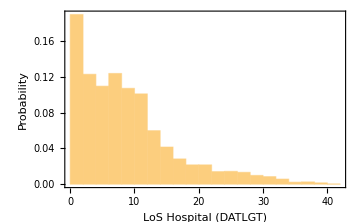

```mathematica
Histogram[DATLGT,Automatic,"Probability",Frame->True,FrameLabel->{"LoS Hospital (DATLGT)","Probability"},ImageSize->Medium]
```

```mathematica
Length/@{DATAD,DATLGT} (*They have the same length due to DATDS is gotten joining the discharge variables to the whole set of cases *)
```

{7132,7132}

```mathematica
(*******************************************************************************)
```

```mathematica
?newDate
```

```mathematica
newDate@DateObject[{2020,5,5},"Day","Gregorian",-5.]
```

05/05/2020

```mathematica
DATAD
```

<|caso527583→Sat 22 Aug 2020,caso527607→Sat 22 Aug 2020,caso527612→Sat 22 Aug 2020,caso527637→Sat 22 Aug 2020,caso527641→Sat 22 Aug 2020,caso527740→Sat 22 Aug 2020,caso527756→Sat 22 Aug 2020,caso527783→Sat 22 Aug 2020,7116,caso837934→Fri 2 Oct 2020,caso837952→Fri 2 Oct 2020,caso838090→Fri 2 Oct 2020,caso838442→Fri 2 Oct 2020,caso838443→Fri 2 Oct 2020,caso838512→Fri 2 Oct 2020,caso840131→,caso841235→Fri 2 Oct 2020|>
 |  |  |  |

```mathematica
DATADh=newDate/@(DATAD/.""->"Missing");
DATADh[[1;;10]] (*Entra al hospital-camaHospital*)
DATDSh=newDate/@DATDS;
DATDSh[[1;;10]](*Se descarga por recuperación, muerte, o tranferencia a otro hosp*)
DATLGTh=day/@(DATLGT/.-""+"Missing"->"Missing");
DATLGTh[[1;;10]](*Tiempo ocupando una cama de hospital*)
```

<|caso527583→22/08/2020,caso527607→22/08/2020,caso527612→22/08/2020,caso527637→22/08/2020,caso527641→22/08/2020,caso527740→22/08/2020,caso527756→22/08/2020,caso527783→22/08/2020,caso528842→02/09/2020,caso528846→22/08/2020|>

<|caso527583→25/08/2020,caso527607→12/09/2020,caso527612→05/09/2020,caso527637→02/09/2020,caso527641→26/08/2020,caso527740→26/08/2020,caso527756→04/09/2020,caso527783→31/08/2020,caso528842→08/09/2020,caso528846→31/08/2020|>

<|caso527583→3,caso527607→5,caso527612→5,caso527637→11,caso527641→4,caso527740→4,caso527756→13,caso527783→9,caso528842→2,caso528846→9|>

#### UCI bed occupation data: DATADI/DATDSI/DATLGTI

```mathematica
(*********************************************)
```

```mathematica
DATADI=masterM[[1,#]]->adUCI[masterM[[All,{1,#}]]]&/@Range[Sequence@@range]//Association;(*Date of admission UCI*)
```

```mathematica
fUCIToCRd=masterM[[1,#]]->fUCIToCR[masterM[[All,{1,#}]]]&/@Range[Sequence@@range]//Association;
```

```mathematica
fUCIToFd=masterM[[1,#]]->fUCIToF[masterM[[All,{1,#}]]]&/@Range[Sequence@@range]//Association;
```

```mathematica
fUCIToHd=masterM[[1,#]]->fUCIToH[masterM[[All,{1,#}]]]&/@Range[Sequence@@range]//Association;
```

```mathematica
DATDSI=Join[cases,DeleteCases[fUCIToCRd,""],DeleteCases[fUCIToFd,""],DeleteCases[fUCIToHd,""]];(*Discharge from UCI*)
```

```mathematica
DATLGTI=DATDSI-DATADI(* Length of stay in UCI*);
```

```mathematica
Length/@{DATDSI,DATADI}
```

{7132,7132}

```mathematica
DATLGTI["caso4563"](* This cases are those who do not have any date of admission and discharge*)
```

Missing[KeyAbsent,caso4563]

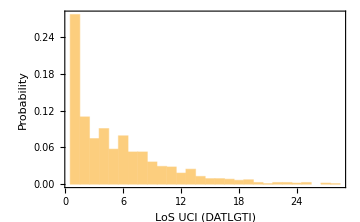

```mathematica
Histogram[DATLGTI,Automatic,"Probability",Frame->True,FrameLabel->{"LoS UCI (DATLGTI)","Probability"},ImageSize->Medium]
```

```mathematica
DATADIh=newDate/@(DATADI/.""->"Missing");
DATADIh[[1;;10]]
DATDSIh=newDate/@DATDSI;
DATDSIh[[1;;10]]
DATLGTIh=day/@(DATLGTI/.-""+"Missing"->"Missing");DATLGTIh[[1;;10]]
```

<|caso527583→Missing,caso527607→27/08/2020,caso527612→27/08/2020,caso527637→Missing,caso527641→Missing,caso527740→Missing,caso527756→Missing,caso527783→Missing,caso528842→04/09/2020,caso528846→Missing|>

<|caso527583→Missing,caso527607→02/09/2020,caso527612→02/09/2020,caso527637→Missing,caso527641→Missing,caso527740→Missing,caso527756→Missing,caso527783→Missing,caso528842→06/09/2020,caso528846→Missing|>

<|caso527583→Missing,caso527607→6,caso527612→6,caso527637→Missing,caso527641→Missing,caso527740→Missing,caso527756→Missing,caso527783→Missing,caso528842→2,caso528846→Missing|>

```mathematica
Length/@{DATADI,DATDSI,DATLGTI}
```

{7132,7132,7132}

#### Calculating Yes/No for Admission: DSXHO / DSXIC

```mathematica
DSXHO=DATAD/.{""->"No",DateObject[___]->"Yes"};
```

```mathematica
DSXIC=DATADI/.{""->"No",DateObject[___]->"Yes"};
```

```mathematica
DSXHOh=DSXHO;DSXHOh[[1;;10]]
DSXICh=DSXIC;DSXICh[[1;;10]]
```

<|caso527583→Yes,caso527607→Yes,caso527612→Yes,caso527637→Yes,caso527641→Yes,caso527740→Yes,caso527756→Yes,caso527783→Yes,caso528842→Yes,caso528846→Yes|>

<|caso527583→No,caso527607→Yes,caso527612→Yes,caso527637→No,caso527641→No,caso527740→No,caso527756→No,caso527783→No,caso528842→Yes,caso528846→No|>

```mathematica
Length/@{DSXHO,DSXIC}
```

{7132,7132}

#### Calculating DSXOS/DATOS

```mathematica
fallecidos=masterM[[1,#]]->estFallecido[masterM[[All,{1,#}]]]&/@Range[Sequence@@range]//Association;
```

```mathematica
recuperado=masterM[[1,#]]->estRecuperado[masterM[[All,{1,#}]]]&/@Range[Sequence@@range]//Association;
```

```mathematica
DSXOS=Join[cases,DeleteCases[fallecidos,"Missing"],DeleteCases[recuperado,"Missing"]];(* Outcome status: Recovered/Deceased *)
```

```mathematica
fallecidos[[1;;10]]
```

<|caso527583→fallecido,caso527607→Missing,caso527612→fallecido,caso527637→Missing,caso527641→fallecido,caso527740→fallecido,caso527756→Missing,caso527783→fallecido,caso528842→fallecido,caso528846→fallecido|>

```mathematica
DSXOS["caso1150"]
```

Missing[KeyAbsent,caso1150]

```mathematica
DSXOSh=(DSXOS/.{"recuperado"->"Recovered","fallecido"->"Deceased"});DSXOSh[[1;;10]]
```

<|caso527583→Deceased,caso527607→Recovered,caso527612→Deceased,caso527637→Recovered,caso527641→Deceased,caso527740→Deceased,caso527756→Recovered,caso527783→Deceased,caso528842→Deceased,caso528846→Deceased|>

```mathematica
Length[DSXOS]
```

7132

```mathematica
(******************************************************************)
```

```mathematica
fallecidosD=masterM[[1,#]]->feFallecido[masterM[[All,{1,#}]]]&/@Range[Sequence@@range]//Association;
```

```mathematica
recuperadoD=masterM[[1,#]]->feRecuperado[masterM[[All,{1,#}]]]&/@Range[Sequence@@range]//Association;
```

```mathematica
fallecidosD//Length
```

7132

```mathematica
fallecidosD[[1;;6]]
```

<|caso527583→Tue 25 Aug 2020,caso527607→,caso527612→Sat 5 Sep 2020,caso527637→,caso527641→Wed 26 Aug 2020,caso527740→Wed 26 Aug 2020|>

```mathematica
DATOS=Join[cases,DeleteCases[fallecidosD,""],DeleteCases[recuperadoD,""]];(* Outcome status: Recovered/Deceased *)
```

```mathematica
DATOSh=newDate/@DATOS;DATOSh[[1;;10]]
```

<|caso527583→25/08/2020,caso527607→13/09/2020,caso527612→05/09/2020,caso527637→03/09/2020,caso527641→26/08/2020,caso527740→26/08/2020,caso527756→06/09/2020,caso527783→31/08/2020,caso528842→08/09/2020,caso528846→31/08/2020|>

```mathematica
Length[DATOSh]
```

7132

#### Fusion of the variables

```mathematica
(* Estoy poniendo Missing cuando no hay datos porque no esta en la base de datos quiza porque no ingresa a UCI o Hopsital o porque no se reportó el dato*)
```

```mathematica
dataBase={{"ID","DATAD","DATADI","DATDSI","DATDS","DATLGT","DATLGTI","DSXHO","DSXIC","DSXOS","DATOS"},Sequence@@Transpose[{cases//Keys,DATADh//Values,DATADIh//Values,DATDSIh//Values,DATDSh//Values,DATLGTh//Values,DATLGTIh//Values,DSXHOh//Values,DSXICh//Values,DSXOSh//Values,DATOSh//Values}]};
```

```mathematica
dataBase//Length
```

7133

```mathematica
masterM[[1]]//Length
```

44132

```mathematica
Export["/home/lina/Documents/datos_INS/dataBase2-9.csv",dataBase,"CSV"]
```

/home/lina/Documents/datos_INS/dataBase2-9.csv

```mathematica
(* "dataBase2-1.csv": 2 a 3000
 "dataBase2-2.csv": 3001 a 7000 
 "dataBase2-3.csv": 7001 a 12000
 "dataBase2-4.csv": 12001 a 17000 
"dataBase2-5.csv": 17001 a 22000 
"dataBase2-6.csv": 22001 a 27000 
"dataBase2-7.csv": 27001 a 32000 
"dataBase2-8.csv": 32001 a 37000 
"dataBase2-9.csv": 37001 a 44132 *)
```

```mathematica
DateObject[{2020,4,6},"Day","Gregorian",-5.]//DateString
```

Mon 6 Apr 2020

```mathematica
{DateObject[{2020,4,6},"Day","Gregorian",-5.],"",DateObject[{2020,4,6},"Day","Gregorian",-5.]}//DateString
```

DateString::arg: Argument {DateObject[{2020,4,6},Day,Gregorian,-5.],,DateObject[{2020,4,6},Day,Gregorian,-5.]} cannot be interpreted as a date or time input or as a date string format.

DateString[{Mon 6 Apr 2020,,Mon 6 Apr 2020}]

```mathematica
"caso1006"->day["Missing"]
```

```mathematica
"Miissng"//DateString
```

Miissng

```mathematica
Quantity[18, "Days"][[1]]
```

```mathematica
18
```

```mathematica
Quantity[18, "Days"]//Normalize
```

1

```mathematica
"Mon 6 Apr 2020"
```

```mathematica
Clear[day]
```

```mathematica
day["Missing"]:="Missing"
day[quantity_/;Head[quantity]==Quantity]:=QuantityMagnitude[quantity]
```

```mathematica
f[""]:=d
```

```mathematica
f[""]
```

d

```mathematica
"caso1006"->day["Missing"]
```

caso1006→day[Missing]

```mathematica
day["Miissng"]
```

Miissng

```mathematica
"Missing"
```

```mathematica
MatchQ[Quantity[18, "Days"],Quantity]
```

False

```mathematica
Quantity[18, "Days"]//Head
```

Quantity